```mathematica
main= {{40.2,26.45},{40.5,28.10},{40.8,31.88},{41.1,27.05},{41.4, 26.18},{40.7,33.1},{40.73,33.58},{40.67,32.1},{40.55,28.8},{40.60,29.82},{40.85,30.3},{40.9,29.1},{41.6,25.9},{41.9,25.68},{38.5,25.38},{39.75,25.8},{36.5,25.2},{44.7,25.2}}
```

{{40.2,26.45},{40.5,28.1},{40.8,31.88},{41.1,27.05},{41.4,26.18},{40.7,33.1},{40.73,33.58},{40.67,32.1},{40.55,28.8},{40.6,29.82},{40.85,30.3},{40.9,29.1},{41.6,25.9},{41.9,25.68},{38.5,25.38},{39.75,25.8},{36.5,25.2},{44.7,25.2}}

```mathematica
zeropos= 25;
amplitude= main[[All,2]]-zeropos
```

{1.45,3.1,6.88,2.05,1.18,8.1,8.58,7.1,3.8,4.82,5.3,4.1,0.9,0.68,0.38,0.8,0.2,0.2}

```mathematica
frequency = main[[All,1]];
```

```mathematica
main1 = Table[{frequency[[i]], amplitude[[i]]},{i,1,Length[amplitude]}]
```

{{40.2,1.45},{40.5,3.1},{40.8,6.88},{41.1,2.05},{41.4,1.18},{40.7,8.1},{40.73,8.58},{40.67,7.1},{40.55,3.8},{40.6,4.82},{40.85,5.3},{40.9,4.1},{41.6,0.9},{41.9,0.68},{38.5,0.38},{39.75,0.8},{36.5,0.2},{44.7,0.2}}

```mathematica
amp= 9;
freq0= 40.73;
```

```mathematica
qq=46.8;
main1= Table[{x,((amp*freq0)/(2*qq))/Sqrt[((x-freq0)^2+((freq0/(2*qq))^2))]+0.1*RandomVariate[NormalDistribution[]]},{x,35,45,0.5}]
```

{{35.,0.661139},{35.5,0.850868},{36.,0.66379},{36.5,0.711367},{37.,0.995685},{37.5,1.22761},{38.,1.45513},{38.5,1.77226},{39.,2.12639},{39.5,2.97806},{40.,4.63666},{40.5,7.91528},{41.,7.63373},{41.5,4.4253},{42.,2.96757},{42.5,2.12542},{43.,1.78099},{43.5,1.35425},{44.,1.22834},{44.5,1.06481},{45.,0.834524}}

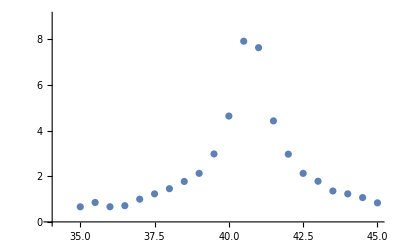

```mathematica
ListPlot[main1,PlotRange->{{34,45},{0,9}}]
```

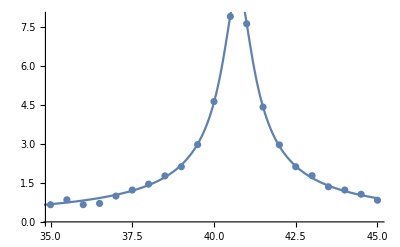

```mathematica
Show[ListPlot[main1],Plot[((amp*freq0)/(2*qq))/Sqrt[((x-freq0)^2+((freq0/(2*qq))^2))],{x,34,45},PlotRange->All]]
```

```mathematica
amp1=9;
freq01 = 40.73;
qq1 = 46.8
fit = NonlinearModelFit[main,((amp1*freq01)/(2*qq1))/Sqrt[((x-freq01)^2+((freq01/(2*qq1))^2))],{{amp1,9},{qq1,46.8},{freq01,40.73}},x]
```

46.8

NonlinearModelFit::fitd: First argument main in NonlinearModelFit is not a list or a rectangular array.

NonlinearModelFit[main,3.91635/(√(0.189355+(-40.73+x)^2)),{{9,9},{46.8,46.8},{40.73,40.73}},x]

```mathematica
fit[{"BestFit","ParameterTable"}]
```

NonlinearModelFit[main,3.91635/(√(0.189355+(-40.73+x)^2)),{{9,9},{46.8,46.8},{40.73,40.73}},x][{BestFit,ParameterTable}]